```mathematica
nMax[pars_]:=Ceiling[2(((-1+s+r s) γ)/(r s)/.pars)]
```

```mathematica
e[i1_,i2_,pars_]:=i1(nMax[pars]+1)+i2+1
```

```mathematica
eback[x_,pars_]:={Floor[(x-1)/(nMax[pars]+1)],Mod[x-1,nMax[pars]+1]}
```

```mathematica
test={r->0.2,γ->12,s->0.99,σ->1,ϵ->0.01,m->0.01,β->1};
```

```mathematica
s>1/(1+r)/.test
```

True

```mathematica
nMax[test]
```

23

```mathematica
tMaxN=1000;ΔtN=50;
```

# The Ecological model

## Deterministic population dynamics

```mathematica
n1=n(1+r (1-n/γ))s+m;
```

```mathematica
Δn=n1-n//Factor;
```

## Equilibria-Exact

```mathematica
Δn
```

(-n^2 r s+m γ-n γ+n s γ+n r s γ)/γ

```mathematica
equi=Solve[(Δn/.θ->1)==0,n]//Simplify
```

{{n→((-1+s+r s) γ-√(γ (4 m r s+(-1+s+r s)^2 γ)))/(2 r s)},{n→((-1+s+r s) γ+√(γ (4 m r s+(-1+s+r s)^2 γ)))/(2 r s)}}

### Biological validity

```mathematica
Reduce[{(n/.equi[[1]])>0,0<γ,0<s<1,0<r,0<m}]//Simplify
```

False

```mathematica
Reduce[{(n/.equi[[2]])>0,0<γ,0<s<1,0<r,0<m}]//Simplify
```

r>0&&0<s<1&&m>0&&γ>0

### Stability

```mathematica
slope=Simplify[D[(Δn/.θ->1),n]/.equi[[2]]]
```

-(√(γ (4 m r s+(-1+s+r s)^2 γ)))/γ

```mathematica
Reduce[{slope<0,0<γ,0<s<1,0<r,0<m}]//Simplify
```

r>0&&0<s<1&&m>0&&γ>0

Equilibrium 2 is always valid and stable

## Equilibria- Approximate (small m)

```mathematica
equA=Simplify[Normal[Series[n/.equi[[2]]/.{m->ms ϵ},{ϵ,0,0}]],Assumptions->{0<γ<1,0<r<1,1/(1+r)<s<1}]
```

((-1+s+r s) γ)/(r s)

## Numerical dynamics

```mathematica
Clear[nEco]
nEco[pars_,tmax_,n0_]:=Block[{out,t},out={{0,n0}};
For[t=1,t≤tmax,t++,
AppendTo[out,{t,n1/.pars/.n->out[[t,2]]}]
];
out
]
```

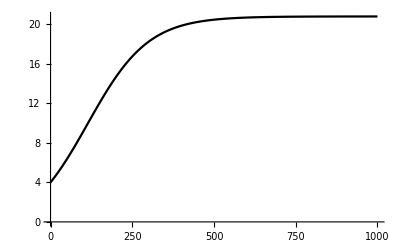

```mathematica
ListLinePlot[nEco[test,tMaxN,4],PlotStyle->Black,PlotRange->All]
```

## Stochastic dynamics

### Initial vector

```mathematica
nInit[pars_]:=Table[1/(nMax[pars]+1),{i,0,nMax[pars]}]
```

```mathematica
nInit[test]
```

{1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41,1/41}

```mathematica
nInit2[pars_,n0_]:=Table[If[i==n0,1,0],{i,0,nMax[pars]}]
```

```mathematica
nInit2[test,4]
```

{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Transition matrix

```mathematica
BMtrx[pars_]:=Block[{out,i,j},out={};
out=Table[0,{j,0,nMax[pars]},{i,0,nMax[pars]}];
For[j=0,j≤nMax[pars],++j,
For[i=0,i ≤ nMax[pars],++i,
If[j≥i&&(i r(1-i/γ)/.pars)>0,out[[j+1,i+1]]=PDF[PoissonDistribution[i r(1-i/γ)],j-i]/.pars]];
];
For[j=0,j≤nMax[pars],++j,
out[[j+1,j+1]]+=1-Total[out[[;;,j+1]]];
];
out
]
```

```mathematica
PDF[PoissonDistribution[λ],x]
```

Piecewise[{{(ⅇ^-λ λ^x)/(x!), x≥0}, {0, True}}]

```mathematica
DMtrx[pars_]:=Block[{out,i,j},out={};
For[j=0,j≤nMax[pars],++j,
AppendTo[out,{}];
For[i=0,i ≤ nMax[pars],++i,
AppendTo[out[[j+1]],
PDF[BinomialDistribution[i,s],j]/.pars];
]
];
out
]
```

```mathematica
MMtrx[pars_]:=Block[{out,i,j},out={};
out=Table[0,{j,0,nMax[pars]},{i,0,nMax[pars]}];
For[j=0,j≤nMax[pars],++j,
For[i=0,i ≤ nMax[pars],++i,
If[j≥i,out[[j+1,i+1]]=PDF[PoissonDistribution[m],j-i]/.pars]];
];
For[j=0,j≤nMax[pars],++j,
out[[j+1,j+1]]+=1-Total[out[[;;,j+1]]];
];
out
]
```

```mathematica
Clear[TMtrx]
TMtrx[pars_]:=TMtrx[pars]=MMtrx[pars].DMtrx[pars].BMtrx[pars]
```

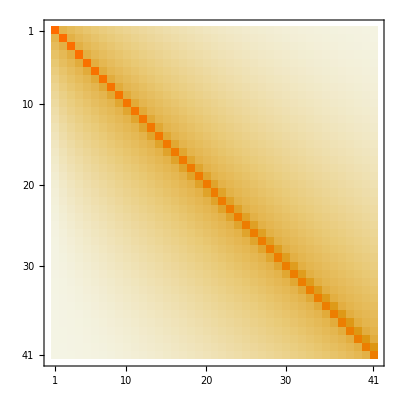

```mathematica
TMtrx[test]//MatrixPlot
```

### Dynamics

```mathematica
state[pars_,n0_,t_]:=MatrixPower[TMtrx[pars],t].nInit2[pars,n0]
```

```mathematica
distPlot1=MatrixPlot[Transpose[Table[0.5-Reverse[state[test,4,i]],{i,0,tMaxN,ΔtN}]],ColorFunction->"GrayTones",FrameTicks->{Table[{i,ToString[nMax[test]-i]},{i,0,nMax[test],5}],Table[{i,ToString[(i-1) ΔtN]},{i,1,tMaxN/ΔtN+1,5}],False,False}];
```

```mathematica
meanPlot1=ListLinePlot[Transpose[{Table[g/ΔtN,{g,0,tMaxN,ΔtN}],Table[state[test,4,g],{g,0,tMaxN,ΔtN}].Table[i,{i,0,nMax[test]}]}],PlotStyle->Red];
```

```mathematica
detPlot1=ListLinePlot[Transpose[{Table[g/ΔtN,{g,0,tMaxN,ΔtN}],Table[nEco[test,tMaxN,4][[g+1,2]],{g,0,tMaxN,ΔtN}]}],PlotStyle->Blue];
```

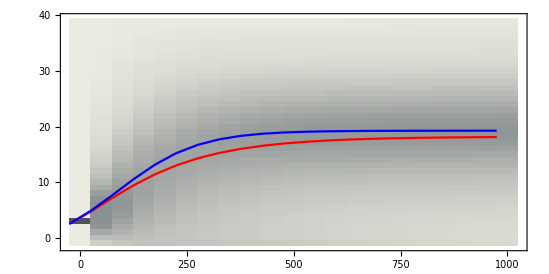

```mathematica
ecoDyn=Show[{distPlot1,meanPlot1,detPlot1},AspectRatio->0.5]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/EcoDyn.gif",ecoDyn,ImageResolution->700]
```

/Users/ailenemacpherson/Documents/OutPut/EcoDyn.gif

### Stationary distribution

```mathematica
Clear[equs,vars]
```

```mathematica
equs[pars_]:=Join[Table[(TMtrx[pars][[2;;,2;;]].Table[Π[i],{i,1,nMax[pars]}])[[j]]+Π[0] TMtrx[pars][[j,1]]==Π[j],{j,1,nMax[pars]}],{Total[Table[Π[i],{i,1,nMax[pars]}]]==1-Π[0]}]
```

```mathematica
vars[pars_]:=Table[Π[i],{i,0,nMax[pars]}]
```

```mathematica
Clear[statDist]
statDist[pars_]:=statDist[pars]=Table[Π[i],{i,0,nMax[pars]}]/.Flatten[Chop[NSolve[equs[pars],vars[pars]]]]
```

```mathematica
statMean=Table[i,{i,0,nMax[test]}].statDist[test]
```

7.03598

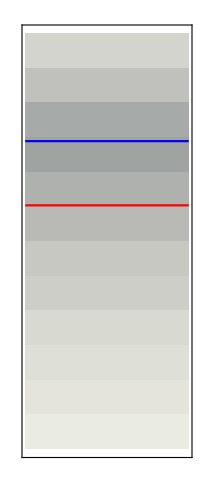

```mathematica
statDistPlot=Show[{MatrixPlot[0.5-Transpose[{Reverse[statDist[test]]}],Frame->True,FrameTicks->{False,False,{{nMax[test]+1,"0"},{nMax[test]-9,"10"},{nMax[test]-4,"5"},{1,ToString[nMax[test]]}},False},ColorFunction->"GrayTones"],ListLinePlot[{{0,statMean},{1,statMean}},PlotStyle->Red],ListLinePlot[{{0,equA/.test},{1,equA/.test}},PlotStyle->Blue]}]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/EcoStatDist.gif",statDistPlot,ImageResolution->700]
```

/Users/ailenemacpherson/Documents/OutPut/EcoStatDist.gif

# Density-independent Selection

## Evolution in an infinite population

```mathematica
np[i_]:=n[i](1+r(1-(n[1]+n[2])/γ))s[i]+m/2;
```

```mathematica
Δn[i_]:=np[i]-n[i]
```

```mathematica
W[i_]:=(1+r(1-(n[1]+n[2])/γ))s[i]
```

## Approximate Equilibria- Weak selection, weak migration

```mathematica
TaylorSub={m->ms ϵ,s[2]->s[1]-σ ϵ,n[1]->n0[1]+ϵ n1[1],n[2]->n0[2]+ϵ n1[2]};
```

```mathematica
equs={Δn[1],Δn[2]};
vars={n[1],n[2]};
```

```mathematica
vars/.TaylorSub/.ϵ->0
```

{n0[1],n0[2]}

```mathematica
varsA=Join[vars/.TaylorSub/.ϵ->0,D[vars/.TaylorSub,ϵ]/.ϵ->0]
```

{n0[1],n0[2],n1[1],n1[2]}

```mathematica
sol0=Solve[(equs/.TaylorSub/.ϵ->0)=={0,0},varsA]//Quiet;
```

```mathematica
sol1[i_]:=Solve[(D[equs/.TaylorSub,ϵ]/.ϵ->0/.sol0[[i]])=={0,0},varsA]//Quiet//Simplify
```

```mathematica
equSub[i_,j_]:=Join[sol0[[i]]/.sol1[i][[j]],sol1[i][[j]]]
```

```mathematica
equSub[1,1]//FullSimplify
```

{n0[2]→(ms r s[1]^2+γ σ (-1+(1+r) s[1])+√(ms^2 r^2 s[1]^4+γ^2 σ^2 (-1+s[1]+r s[1])^2))/(2 r σ s[1]),n0[1]→-(γ σ-(1+r) γ σ s[1]+ms r s[1]^2+√(ms^2 r^2 s[1]^4+γ^2 σ^2 (-1+(1+r) s[1])^2))/(2 r σ s[1]),n1[2]→-((γ σ (-1+(1+r) s[1])-r s[1]^2 (ms-2 n1[1] (-1+(1+r) s[1]))+√(ms^2 r^2 s[1]^4+γ^2 σ^2 (-1+(1+r) s[1])^2))/(2 r s[1]^2 (-1+(1+r) s[1])))}

```mathematica
equSub[1,2]
```

{n0[2]→(γ (-1+s[1]+r s[1]))/(r s[1])-(-ms r s[1]^2+γ σ (-1+(1+r) s[1])+√(ms^2 r^2 s[1]^4+γ^2 σ^2 (-1+(1+r) s[1])^2))/(2 r σ s[1]),n0[1]→(-ms r s[1]^2+γ σ (-1+(1+r) s[1])+√(ms^2 r^2 s[1]^4+γ^2 σ^2 (-1+(1+r) s[1])^2))/(2 r σ s[1]),n1[2]→(ms r s[1]^2+2 r n1[1] s[1]^2-2 r n1[1] s[1]^3-2 r^2 n1[1] s[1]^3-γ σ (-1+(1+r) s[1])+√(ms^2 r^2 s[1]^4+γ^2 σ^2 (-1+(1+r) s[1])^2))/(2 r s[1]^2 (-1+(1+r) s[1]))}

```mathematica
equSub[2,1]
```

{n0[1]→0,n0[2]→0,n1[1]→ms/(2-2 s[1]-2 r s[1]),n1[2]→ms/(2-2 s[1]-2 r s[1])}

### Biological Validity

#### Equilibrium 1: Never valid

```mathematica
Reduce[{(n0[1]/.equSub[1,1])>0,0<r,0<s[1]<1,0<σ<1,0<ms,0<γ}]
```

False

```mathematica
Reduce[{(n0[2]/.equSub[1,1])>0,0<r,0<s[1]<1,0<σ<1,0<ms,0<γ}]
```

0<s[1]<1&&0<σ<1&&r>0&&γ>0&&ms>0

#### Equilibrium 2: Valid when 1/(1+r)<s[1]

```mathematica
Reduce[{(n0[1]/.equSub[1,2])>0,0<r,0<s[1]<1,0<σ<1,0<ms,0<γ},s[1]]
```

0<σ<1&&r>0&&ms>0&&γ>0&&1/(1+r)<s[1]<1

```mathematica
Reduce[{(n0[2]/.equSub[1,2])>0,0<r,0<s[1]<1,0<σ<1,0<ms,0<γ},s[1]]
```

0<σ<1&&r>0&&ms>0&&γ>0&&1/(1+r)<s[1]<1

#### Equilibrium 3: Never valid

```mathematica
Reduce[{(n0[1]/.equSub[2,1])>0,0<r,0<s[1]<1,0<σ<1,0<ms,0<γ},s[1]]
```

False

```mathematica
Reduce[{(n0[1]/.equSub[2,1])>0,0<r,0<s[1]<1,0<σ<1,0<ms,0<γ},s[1]]
```

False

### Stability

```mathematica
jmtrx={{D[Δn[1],n[1]],D[Δn[1],n[2]]},{D[Δn[2],n[1]],D[Δn[2],n[2]]}}/.TaylorSub;
```

#### Equilibrium 1: Only possibly stable when d<r/(1+r)

```mathematica
CP=CharacteristicPolynomial[jmtrx,λ]/.equSub[1,1];
```

```mathematica
λsol=Solve[Simplify[CP/.ϵ->0]==0,λ]
```

{{λ→0},{λ→d-r+d r}}

```mathematica
Reduce[{(λ/.λsol[[2]])<0,0<d<1,0<r}]
```

r>0&&0<d<r/(1+r)

#### Equilibrium 3: Stable if r/(1+r)<d

```mathematica
CP=CharacteristicPolynomial[jmtrx,λ]/.equSub[2,1];
```

```mathematica
λsol=Solve[Simplify[CP/.ϵ->0]==0,λ]
```

{{λ→-d+r-d r},{λ→-d+r-d r}}

```mathematica
Reduce[{(λ/.λsol[[1]])<0,(λ/.λsol[[2]])<0,0<d<1,0<r}]
```

r>0&&r/(1+r)<d<1

## Migration Selection model

```mathematica
p1=(1+s)/(p(1+s)+(1-p))p;
p2=(1-m)p1+m/2;
```

```mathematica
psol=Solve[p2-p==0,p]
```

{{p→(-2 m+2 s-m s+√(8 m s+(-2 m+2 s-m s)^2))/(4 s)},{p→-(2 m-2 s+m s+√(8 m s+(-2 m+2 s-m s)^2))/(4 s)}}

```mathematica
Series[(p/.psol[[1]]/.{m->ϵ μ,s->ϵ σ}),{ϵ,0,0}]
```

(-μ+σ+√(μ^2+σ^2))/(2 σ)+O[ϵ]^1

```mathematica
Series[(p/.psol[[2]]/.{m->ϵ μ,s->ϵ σ}),{ϵ,0,0}]
```

(-μ+σ-√(μ^2+σ^2))/(2 σ)+O[ϵ]^1

```mathematica
n0[1]/(n0[1]+n0[2])/.equSub[1,2]//FullSimplify
```

(-ms r s[1]^2+γ σ (-1+(1+r) s[1])+√(ms^2 r^2 s[1]^4+γ^2 σ^2 (-1+s[1]+r s[1])^2))/(2 γ σ (-1+(1+r) s[1]))

```mathematica
num=-ms r s[1]^2+γ σ (-1+(1+r) s[1]);
denom=2 γ σ (-1+(1+r) s[1]);
arg=ms^2 r^2 s[1]^4+γ^2 σ^2 (-1+s[1]+r s[1])^2;
```

```mathematica
σsub={σ->denom/2}//Simplify
```

{σ→γ σ (-1+(1+r) s[1])}

```mathematica
μsub={μ-> Simplify[denom/2-num]}
```

{μ→ms r s[1]^2}

```mathematica
((μ^2+σ^2)/.σsub/.μsub)-(arg)//Simplify
```

0

## Numerical Dynamics

```mathematica
nDyn[pars_,n0_,tmax_]:=Block[{out,t},out={Join[{0},n0]};
For[t=1,t≤tmax,t++,
AppendTo[out,{t,np[1],np[2]}/.{d[1]->d,d[2]->d+δ ϵ}/.pars/.{n[1]->out[[t,2]],n[2]->out[[t,3]]}]
];
out
]
```

```mathematica
tmaxN=100 ; ΔtN=5;
```

```mathematica
tMaxP=500;ΔtP=5;
```

```mathematica
ndy=nDyn[test,{2,2},tMaxP];
```

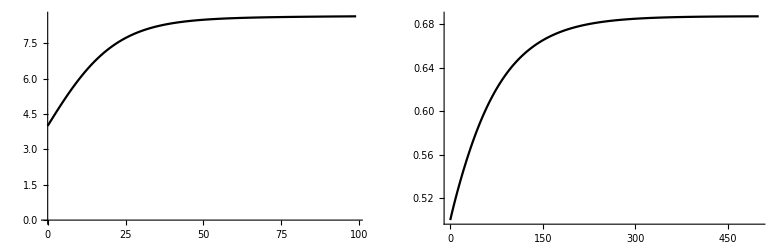

```mathematica
GraphicsRow[{ListLinePlot[Transpose[{ndy[[1;;tmaxN,1]],ndy[[1;;tmaxN,2]]+ndy[[1;;tmaxN,3]]}],PlotRange->All,PlotStyle->Black,ImageSize->Medium],ListLinePlot[Transpose[{ndy[[;;,1]],ndy[[;;,2]]/(ndy[[;;,2]]+ndy[[;;,3]])}],PlotRange->All,PlotStyle->Black,ImageSize->Medium]}]
```

## Evolution in a finite population

### Initial vector

```mathematica
vec0[pars_]:=Block[{out,i1,i2},out={};
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤ nMax[pars],i2++, 
AppendTo[out,1/(nMax[pars]+1)^2];
]
];
out//N
]
```

```mathematica
vec02[pars_,n0_]:=Block[{out,i1,i2},out={};
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤ nMax[pars],i2++,
If[i1==n0[[1]]&&i2==n0[[2]],AppendTo[out,1],AppendTo[out,0]];
]
];
out//N
]
```

### vector to matrix

```mathematica
v2m[pars_,vIn_]:=Block[{out2,i1,i2,ct},out2=Table[0,{i1,0,nMax[pars]},{i2,0,nMax[pars]}];ct=1;
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤nMax[pars],i2++,
out2[[i1+1,i2+1]]=vIn[[ct]];
ct++;
];
];
out2
]
```

### Transition matrix

```mathematica
BMtrx[pars_]:=Block[{out,i1,j1,i2,j2,k,b1,b2},out={};
out=Table[0,{j,1,(1+nMax[pars])^2},{i,1,(1+nMax[pars])^2}];
For[j1=0,j1≤nMax[pars],++j1,
For[i1=0,i1 ≤ nMax[pars],++i1,
For[j2=0,j2≤nMax[pars],++j2,
For[i2=0,i2 ≤ nMax[pars],++i2,
If[j1≥i1&&j2≥i2,
b1=If[(i1 r(1-(i1+i2)/γ)/.pars)>0,PDF[PoissonDistribution[i1 r(1-(i1+i2)/γ)],j1-i1],If[j1==0,1,0]];
b2=If[(i2 r(1-(i1+i2)/γ)/.pars)>0,PDF[PoissonDistribution[i2 r(1-(i1+i2)/γ)],j2-i2],If[j2==0,1,0]];
out[[e[j1,j2,pars],e[i1,i2,pars]]]=b1 b2/.pars]
]]]];
For[k=1,k≤(1+nMax[pars])^2,++k,
out[[k,k]]+=1-Total[out[[;;,k]]];
];
out//Chop
]
```

```mathematica
DMtrx[pars_]:=Block[{out,i1,j1,i2,j2},out={};
out=Table[0,{j,1,(1+nMax[pars])^2},{i,1,(1+nMax[pars])^2}];
For[j1=0,j1≤nMax[pars],++j1,
For[i1=0,i1 ≤ nMax[pars],++i1,
For[j2=0,j2≤nMax[pars],++j2,
For[i2=0,i2 ≤ nMax[pars],++i2,
If[j1≤i1&&j2≤i2,out[[e[j1,j2,pars],e[i1,i2,pars]]]=PDF[BinomialDistribution[i1,s],j1]PDF[BinomialDistribution[i2,s-σ ϵ],j2]/.pars]
]]]];
out//Chop
]
```

```mathematica
MMtrx[pars_]:=Block[{out,i1,j1,i2,j2,k},out={};
out=Table[0,{j,1,(1+nMax[pars])^2},{i,1,(1+nMax[pars])^2}];
For[j1=0,j1≤nMax[pars],++j1,
For[i1=0,i1 ≤ nMax[pars],++i1,
For[j2=0,j2≤nMax[pars],++j2,
For[i2=0,i2 ≤ nMax[pars],++i2,
If[j1≥i1&&j2≥i2,out[[e[j1,j2,pars],e[i1,i2,pars]]]=PDF[PoissonDistribution[m/2],j1-i1]PDF[PoissonDistribution[m/2],j2-i2]/.pars]
]]]];
For[k=1,k≤(1+nMax[pars])^2,++k,
out[[k,k]]+=1-Total[out[[;;,k]]];
];
out//Chop
]
```

```mathematica
TMtrx[pars_]:=TMtrx[pars]=Chop[MMtrx[pars].DMtrx[pars].BMtrx[pars]]
```

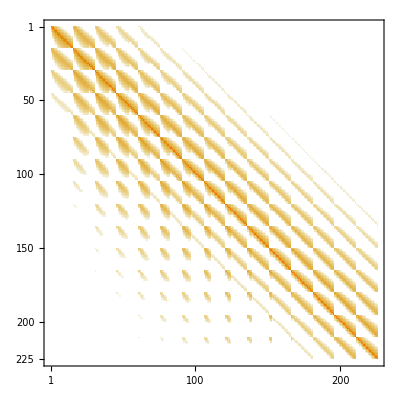

```mathematica
MatrixPlot[TMtrx[test]]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/sparse.gif",MatrixPlot[TMtrx[test]],ImageResolution->700]
```

/Users/ailenemacpherson/Documents/OutPut/sparse.gif

### Stochastic dynamics

#### Functions

```mathematica
state[pars_,t_,n0_]:=state[pars,t,n0]=v2m[pars,MatrixPower[TMtrx[pars],t].vec02[pars,n0]]
```

```mathematica
nTot[pars_,t_,n0_]:=Block[{out,x},out={};
For[x=0,x≤nMax[pars],x++,
AppendTo[out,Sum[state[pars,t,n0][[i+1,x-i+1]],{i,0,x}]]
];
out
]
```

```mathematica
nTotAvg[pars_,t_,n0_]:=Block[{out,i,j},
out=0;
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
out+=(i+j)state[pars,t,n0][[i+1,j+1]]
];
];
out
]
```

```mathematica
AF2[pars_,t_,n0_]:=Block[{out,i,j},
out=Table[0,{i,1,10}];
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
If[i+j≠0,
out[[If[i==0,1,Round[(10i)/(i+j)]]]]+=state[pars,t,n0][[i+1,j+1]];
]
];
];
out
]
```

```mathematica
AFAvg[pars_,t_,n0_]:=Block[{out,i,j},
out = 0;
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
If[i+j≠0,
out +=(i/(i+j))state[pars,t,n0][[i+1,j+1]];
]
];
];
out
]
```

#### Plots

```mathematica
meanP1=ListLinePlot[Table[{t/ΔtN,nTotAvg[test,t,{2,2}]},{t,0,tmaxN,ΔtN}],PlotRange->All,PlotStyle->Red];
```

```mathematica
detP1=ListLinePlot[Table[{i/ΔtN,(ndy[[i+1,2]]+ndy[[i+1,3]])},{i,0,tmaxN,ΔtN}],PlotRange->All,PlotStyle->Blue];
```

```mathematica
distP1=MatrixPlot[Transpose[Table[0.5-Reverse[nTot[test,t,{2,2}]],{t,0,tmaxN,ΔtN}]],ColorFunction->"GrayTones"];
```

```mathematica
distP2=MatrixPlot[Transpose[Table[0.5-Reverse[AF2[test,t,{2,2}]],{t,0,tMaxP,ΔtP}]],PlotRange->{{0,10},{0,tMaxP/ΔtP}},AspectRatio->0.5, ColorFunction->"GrayTones"];
```

```mathematica
meanP2=ListLinePlot[Table[{t/ΔtP,10 AFAvg[test,t,{2,2}]},{t,0,tMaxP,ΔtP}],PlotStyle->Red,PlotRange->{Automatic,{0,10}}];
```

```mathematica
detP2=ListLinePlot[Table[{i/ΔtP,10 ndy[[i+1,2]]/(ndy[[i+1,2]]+ndy[[i+1,3]])},{i,0,tMaxP,ΔtP}],PlotRange->All,PlotStyle->Blue];
```

#### Combined Plots

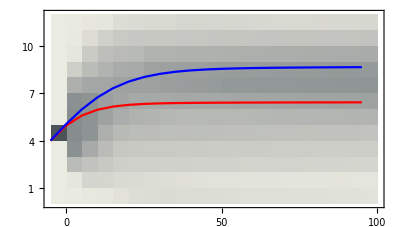

```mathematica
Show[{distP1,meanP1,detP1},FrameTicks->{Table[{t/ΔtN+1,ToString[t]},{t,0,tmaxN,ΔtN*10}],Table[{i,ToString[i]},{i,1,nMax[test],3}],False,False}]
```

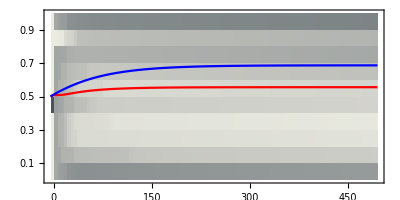

```mathematica
Show[{distP2,meanP2,detP2},FrameTicks->{Table[{t/ΔtP+1,ToString[t]},{t,0,tMaxP,10*ΔtP}],Table[{i,ToString[N[i/10]]},{i,1,10,2}],False,False}]
```

### Stationary distribution

#### Calculating Stationary Distribution

```mathematica
Clear[equs,vars]
equs[pars_]:=Join[Table[(TMtrx[pars][[2;;,2;;]].Table[Π[i],{i,2,(1+nMax[pars])^2}])[[j-1]]+Π[1] TMtrx[pars][[j-1,1]]==Π[j],{j,2,(1+nMax[pars])^2}],{Total[Table[Π[i],{i,2,(1+nMax[pars])^2}]]==1-Π[1]}]
vars[pars_]:=Table[Π[i],{i,1,(1+nMax[pars])^2}]
```

```mathematica
Clear[statDist]
statDist[pars_]:=statDist[pars]=Table[Π[i],{i,1,(1+nMax[pars])^2}]/.Flatten[Chop[NSolve[equs[pars],vars[pars]]]]
```

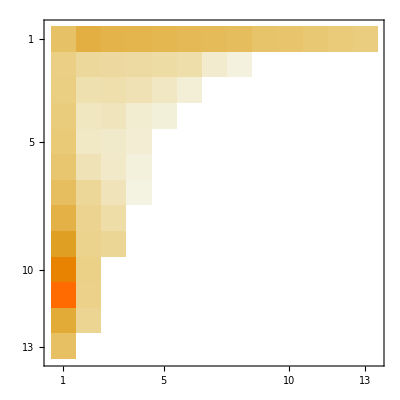

```mathematica
v2m[test,statDist[test]]//MatrixPlot
```

#### Functions

```mathematica
nAvg[vec_,pars_]:=Block[{i1,i2,n1,n2},n1=0;n2=0;
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤nMax[pars],i2++,
n1+=vec[[e[i1,i2,pars]]]i1;
n2+=vec[[e[i1,i2,pars]]]i2;
]
];
{n1,n2}
]
```

```mathematica
nAvg[statDist[test],test]
```

{8.79904,0.216845}

```mathematica
nTotVec[pars_]:=Block[{statM,i,j,out},out=Table[0,{i,0,2nMax[pars]}];
statM=v2m[pars,statDist[pars]];
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
out[[i+j+1]]+=statM[[i+1,j+1]]
];
];
out
]
```

```mathematica
nTotStatAvg=nTotVec[test].Table[i,{i,0,2nMax[test]}];
```

```mathematica
nTotEquDet=n0[1]+n0[2]/.equSub[1,1]/.test;
```

```mathematica
pVec[pars_]:=Block[{statM,i,j,out},out=Table[0,{i,1,10}];
statM=v2m[pars,statDist[pars]];
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
out[[If[i==0,1,Round[10 i/(i+j)]]]]+=statM[[i+1,j+1]]
];
];
out
]
```

```mathematica
pMean[pars_]:=Block[{statM,i,j,out},out=0;
statM=v2m[pars,statDist[pars]];
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
If[i+j≠0,
out+=i/(i+j)statM[[i+1,j+1]]
]
];
];
out
]
```

```mathematica
pDet=n0[1]/(n0[1]+n0[2])/.equSub[1,1]/.{ms->ϵ m}/.test
```

1.

#### Plots

```mathematica
distP=MatrixPlot[Transpose[{Reverse[0.5-nTotVec[test][[1;;nMax[test]+1]]]}],ColorFunction->"GrayTones"];
```

```mathematica
meanP=ListLinePlot[{{0,nTotStatAvg},{1,nTotStatAvg}},PlotStyle->Red,PlotRange->{1,nMax[test]+1}];
```

```mathematica
detP=ListLinePlot[{{0,nTotEquDet},{1,nTotEquDet}},PlotStyle->Blue,PlotRange->{1,nMax[test]+1}];
```

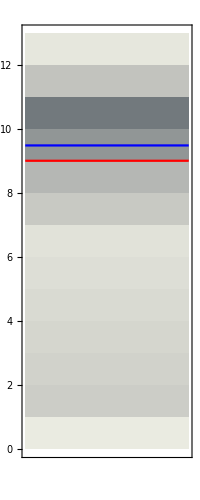

```mathematica
Show[{distP,meanP,detP},FrameTicks->{False,Table[{i,ToString[i]},{i,0,nMax[test]}],False,False}]
```

```mathematica
distP=MatrixPlot[Transpose[{Reverse[0.5-pVec[test]]}],ColorFunction->"GrayTones"];
```

```mathematica
meanP=ListLinePlot[{{0,10pMean[test]},{1,10pMean[test]}},PlotStyle->Red,PlotRange->{0,10}];
```

```mathematica
detP=ListLinePlot[{{0,10pDet},{1,10pDet}},PlotStyle->Blue,PlotRange->{0,10}];
```

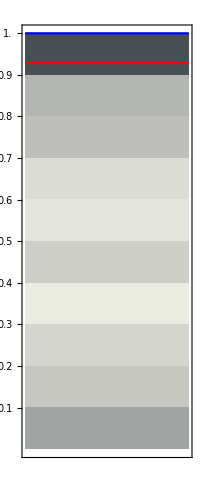

```mathematica
Show[{distP,detP,meanP},FrameTicks->{False,Table[{i,ToString[N[i/10]]},{i,1,10}],False,False}]
```

## Finite vs. Infinite dynamics

# Density-dependent Selection

## Constraints on r and k

```mathematica
np[i_]:=n[i](1+r[i](1-(n[1]+n[2])/γ[i]))s+m/2;
```

```mathematica
Δn[i_]:=np[i]-n[i]
```

We can define a trade-off such that r[i]γ[i]^(1/β)=constant.  If we have a baseline genotype i=0 with growth rate of r[0] and growth limit of γ[0] then a genotype i with a growth rate r[i] must have a growth limit of:

```mathematica
Solve[{r[0] γ[0]^(1/β)==r[i] γ[i]^(1/β)},γ[i]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ[i]→((r[0] γ[0]^(1/β))/r[i])^β}}

```mathematica
Clear[tOffSub]
```

```mathematica
tOffSub[i_]:={γ[i]->γ[0](r[0]/r[i])^β};
```

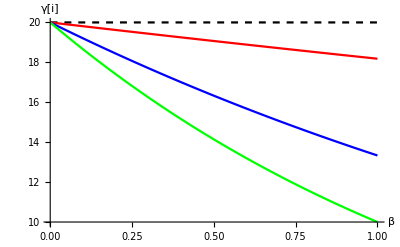

```mathematica
Plot[{γ[0]/.{r[0]->0.1,γ[0]->20,r[i]->0.2},γ[0](r[0]/r[i])^β/.{r[0]->0.1,γ[0]->20,r[i]->0.11},γ[0](r[0]/r[i])^β/.{r[0]->0.1,γ[0]->20,r[i]->0.15},γ[0](r[0]/r[i])^β/.{r[0]->0.1,γ[0]->20,r[i]->0.2}},{β,0.001,1},PlotStyle->{{Black,Dashed},{Red},{Blue},{Green}},AxesLabel->{"β","γ[i]"}]
```

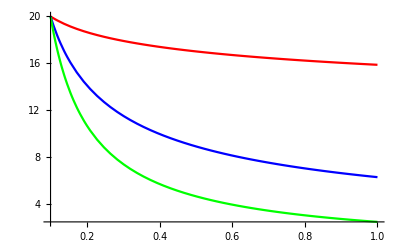

```mathematica
tradeOffPlot=Plot[{γ[0](r[0]/x)^β/.{r[0]->0.1,γ[0]->20,β->0.1},γ[0](r[0]/x)^β/.{r[0]->0.1,γ[0]->20,β->0.5},γ[0](r[0]/x)^β/.{r[0]->0.1,γ[0]->20,β->0.9}},{x,0.1,1},PlotRange->All,PlotStyle->{Red,Blue,Green}]
```

```mathematica
(*Export["/Users/ailenemacpherson/Documents/Output/tradeoff.gif",tradeOffPlot,ImageResolution->700]*)
```

## Evolution in an infinite population

```mathematica
np[i_]:=n[i](1+r[i](1-(n[1]+n[2])/γ[i]))s+m/2;
```

```mathematica
Δn[i_]:=np[i]-n[i]
```

```mathematica
W[i_]:=(1+r[i](1-(n[1]+n[2])/γ[i]))s
```

```mathematica
W[1]/(p W[1]+q W[2])/.tOffSub[1]/.tOffSub[2]//FullSimplify;
```

```mathematica
equs={Δn[1],Δn[2]};
```

```mathematica
vars={n[1],n[2]};
```

## Approximate Equilibria-Weak selection and migration

```mathematica
TaylorSubTradeOff={m->ms ϵ,r[1]->r[0],r[2]->r[0]+σ ϵ,n[1]->n0[1]+ϵ n1[1],n[2]->n0[2]+ϵ n1[2]};
```

```mathematica
varsA=Join[vars/.TaylorSubTradeOff/.ϵ->0,D[vars/.TaylorSubTradeOff,ϵ]/.ϵ->0];
```

```mathematica
sol0=Solve[((equs/.tOffSub[1]/.tOffSub[2]/.TaylorSubTradeOff)/.ϵ->0)=={0,0},varsA]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{n0[2]→-n0[1]+((-1+s+s r[0]) γ[0])/(s r[0])},{n0[1]→0,n0[2]→0}}

```mathematica
sol1[i_]:=Solve[(D[(equs/.tOffSub[1]/.tOffSub[2]/.TaylorSubTradeOff),ϵ]/.sol0[[i]]/.ϵ->0)=={0,0},varsA]//FullSimplify
```

```mathematica
equSub[i_,j_]:=Join[sol0[[i]]/.sol1[i][[j]],sol1[i][[j]]]
```

```mathematica
equSub[1,2]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{n0[2]→((-1+s+s r[0]) γ[0])/(s r[0])-(-ms s r[0]^2+σ (-1+s+s r[0]) ((-1+s) (1+β)+s β r[0]) γ[0]+√(ms^2 s^2 r[0]^4+σ^2 (-1+s+s r[0])^2 ((-1+s) (1+β)+s β r[0])^2 γ[0]^2))/(2 s σ r[0] ((-1+s) (1+β)+s β r[0])),n0[1]→(-ms s r[0]^2+σ (-1+s+s r[0]) ((-1+s) (1+β)+s β r[0]) γ[0]+√(ms^2 s^2 r[0]^4+σ^2 (-1+s+s r[0])^2 ((-1+s) (1+β)+s β r[0])^2 γ[0]^2))/(2 s σ r[0] ((-1+s) (1+β)+s β r[0])),n1[2]→1/(2 s r[0]^2 (-1+s+s r[0]))(ms s r[0]^2+(-1+s+s r[0]) (-2 s n1[1] r[0]^2-σ ((-1+s) (1+β)+s β r[0]) γ[0])+√(ms^2 s^2 r[0]^4+σ^2 (-1+s+s r[0])^2 ((-1+s) (1+β)+s β r[0])^2 γ[0]^2))}

### Biological Validity

#### Equilibrium 1: Never valid.

```mathematica
Reduce[{(n0[1]/.equSub[1,1])>0,(n0[2]/.equSub[1,1])>0,0<s<1,0<γ[0],0<r[0],0<β,0<σ,0<ms}]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

False

#### Equilibrium 2: Valid if 1/(1+r[0])<s

```mathematica
Reduce[{(n0[1]/.equSub[1,2])>0,(n0[2]/.equSub[1,2])>0,0<s<1,0<γ[0],0<r[0],0<β,0<σ,0<ms}]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

(0<β<(1-s)/(-1+s+s r[0])||β>(1-s)/(-1+s+s r[0]))&&1/(1+r[0])<s<1&&ms>0&&σ>0&&r[0]>0&&γ[0]>0

#### Equilibrium 3: Valid if s<1/(1+r[0])

```mathematica
Reduce[{(n1[1]/.equSub[2,1])>0,(n1[2]/.equSub[2,1])>0,0<s<1,0<γ[0],0<r[0],0<β,0<σ,0<ms}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

β>0&&σ>0&&γ[0]>0&&r[0]>0&&0<s<1/(1+r[0])&&ms>0

### Stability

```mathematica
jmtrx={{D[Δn[1],n[1]],D[Δn[1],n[2]]},{D[Δn[2],n[1]],D[Δn[2],n[2]]}};
```

```mathematica
TaylorSubTradeOff
```

{m→ms ϵ,r[1]→r[0],r[2]→δ ϵ+r[0],n[1]→n0[1]+ϵ n1[1],n[2]→n0[2]+ϵ n1[2]}

```mathematica
CP=CharacteristicPolynomial[jmtrx,λ]/.tOffSub[1]/.tOffSub[2]/.TaylorSubTradeOff;
```

```mathematica
λsol=Solve[Simplify[CP/.ϵ->0]==0,λ]//FullSimplify
```

{{λ→r[0]-d (1+r[0])+((-1+d) (n0[1]+n0[2]) r[0])/γ[0]},{λ→r[0]-d (1+r[0])+(2 (-1+d) (n0[1]+n0[2]) r[0])/γ[0]}}

#### Equilibrium 2: Stable if d<r[0]/(1+r[0])

```mathematica
(λsol/.equSub[1,2])//Simplify
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Part at positions 1 and 2 are expected to be the same.

{{λ→r[0]-d (1+r[0])+((-1+d) (n0[1]+n0[2]) r[0])/γ[0]},{λ→r[0]-d (1+r[0])+(2 (-1+d) (n0[1]+n0[2]) r[0])/γ[0]}}/.Join[{}⟦1⟧/.{}⟦2⟧,{}⟦2⟧]

The first-order stability analysis is inconclusive but the equilibrium is guarenteed to be unstable if:

```mathematica
Reduce[{(λ/.λsol[[2]]/.equSub[1,2])>0,0<d<1,0<γ[0],0<r[0]}]//Simplify
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Part at positions 1 and 2 are expected to be the same.

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{(r[0]-d (1+r[0])+(2 (-1+d) (n0[1]+n0[2]) r[0])/γ[0]/.Join[{}⟦1⟧/.{}⟦2⟧,{}⟦2⟧])>0,0<d<1,γ[0]>0,r[0]>0}]

To the second order for λ=0+O(ϵ)

```mathematica
λ1equ=D[(CP/.equSub[1,2]/.λ->λ0+λ1 ϵ),ϵ]/.ϵ->0/.λ0->0//Simplify
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Part at positions 1 and 2 are expected to be the same.

General::ivar: 0 is not a valid variable.

∂_0 (1/γ[0]^2(2 (-1+d)^2 n0[1]^2 r[0]^2+2 (-1+d)^2 n0[2]^2 r[0]^2-3 (-1+d) n0[2] r[0] (d-r[0]+d r[0]) γ[0]+(d-r[0]+d r[0])^2 γ[0]^2+(-1+d) n0[1] r[0] (4 (-1+d) n0[2] r[0]-3 (d-r[0]+d r[0]) γ[0]))/.Join[{}⟦1⟧/.{}⟦2⟧,{}⟦2⟧])

```mathematica
λ1sol=λ1/.Flatten[Solve[λ1equ==0,λ1]]
```

λ1

```mathematica
Reduce[{λ1sol<0,0<d<1,0<γ[0],0<r[0],0<ms,0<β,0<δ}]
```

δ>0&&λ1<0&&β>0&&r[0]>0&&ms>0&&γ[0]>0&&0<d<1

#### Equilibrium 3: Stable if r[0]/(1+r[0])<d

```mathematica
(λsol/.equSub[2,1])//Simplify
```

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Part at positions 1 and 2 are expected to be the same.

{{λ→r[0]-d (1+r[0])+((-1+d) (n0[1]+n0[2]) r[0])/γ[0]},{λ→r[0]-d (1+r[0])+(2 (-1+d) (n0[1]+n0[2]) r[0])/γ[0]}}/.Join[{}⟦2⟧/.{}⟦1⟧,{}⟦1⟧]

```mathematica
Reduce[{(λ/.λsol[[1]]/.equSub[2,1])<0,(λ/.λsol[[2]]/.equSub[2,1])<0,0<d<1,0<γ[0],0<r[0]}]
```

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Part at positions 1 and 2 are expected to be the same.

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{(r[0]-d (1+r[0])+((-1+d) (n0[1]+n0[2]) r[0])/γ[0]/.Join[{}⟦2⟧/.{}⟦1⟧,{}⟦1⟧])<0,(r[0]-d (1+r[0])+(2 (-1+d) (n0[1]+n0[2]) r[0])/γ[0]/.Join[{}⟦2⟧/.{}⟦1⟧,{}⟦1⟧])<0,0<d<1,0<γ[0],0<r[0]}]

## Numerical dynamics- r/K trade off

```mathematica
nDyn[pars_,n0_,tmax_]:=Block[{out,t},out={Join[{0},n0]};
For[t=1,t≤tmax,t++,
AppendTo[out,{t,np[1],np[2]}/.tOffSub[1]/.tOffSub[2]/.{γ[0]->γ,r[0]->r,r[1]->r,r[2]->r+δ ϵ}/.pars/.{n[1]->out[[t,2]],n[2]->out[[t,3]]}]
];
out
]
```

```mathematica
tmaxN=100;tmaxP=500;ΔtN=5;ΔtP=10;
```

```mathematica
ndy2=nDyn[test,{2,2},tmaxP];
```

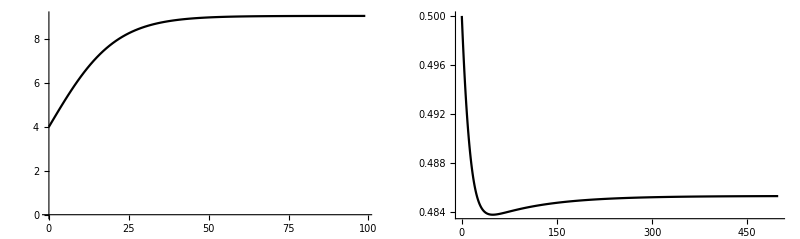

```mathematica
GraphicsRow[{ListLinePlot[Transpose[{ndy2[[1;;tmaxN,1]],ndy2[[1;;tmaxN,2]]+ndy2[[1;;tmaxN,3]]}],PlotRange->All,PlotStyle->Black],ListLinePlot[Transpose[{ndy2[[1;;tmaxP,1]],ndy2[[1;;tmaxP,2]]/(ndy2[[1;;tmaxP,2]]+ndy2[[1;;tmaxP,3]])}],PlotRange->All,PlotStyle->Black]}]
```

## Migration Selection model

```mathematica
p1=(1+s)/(p(1+s)+(1-p))p;
p2=(1-m)p1+m/2;
```

```mathematica
psol=Solve[p2-p==0,p]
```

{{p→(-2 m+2 s-m s+√(8 m s+(-2 m+2 s-m s)^2))/(4 s)},{p→-(2 m-2 s+m s+√(8 m s+(-2 m+2 s-m s)^2))/(4 s)}}

```mathematica
Series[(p/.psol[[1]]/.{m->ϵ μ,s->ϵ σ}),{ϵ,0,0}]
```

(-μ+σ+√(μ^2+σ^2))/(2 σ)+O[ϵ]^1

```mathematica
Series[(p/.psol[[2]]/.{m->ϵ μ,s->ϵ σ}),{ϵ,0,0}]
```

(-μ+σ-√(μ^2+σ^2))/(2 σ)+O[ϵ]^1

```mathematica
num=(-1+d) ms r[0]^2+δ (d+(-1+d) r[0]) (d (1+β)+(-1+d) β r[0]) γ[0];
denom=(2 δ (d-r[0]+d r[0]) (d (1+β)+(-1+d) β r[0]) γ[0]);
arg=(-1+d)^2 ms^2 r[0]^4+δ^2 (d+(-1+d) r[0])^2 (d (1+β)+(-1+d) β r[0])^2 γ[0]^2;
```

```mathematica
σsub={σ->denom/2}//Simplify
```

{σ→δ (d-r[0]+d r[0]) (d (1+β)+(-1+d) β r[0]) γ[0]}

```mathematica
μsub={μ-> Simplify[denom/2-num]}
```

{μ→-(-1+d) ms r[0]^2}

```mathematica
arg-(μ^2+σ^2)/.σsub/.μsub//Simplify
```

0

## Evolution in a finite population 2

### Initial vector

```mathematica
vec0[pars_]:=Block[{out,i1,i2},out={};
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤ nMax[pars],i2++, 
AppendTo[out,1/(nMax[pars]+1)^2];
]
];
out//N
]
```

```mathematica
vec02[pars_,n0_]:=Block[{out,i1,i2},out={};
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤ nMax[pars],i2++,
If[i1==n0[[1]]&&i2==n0[[2]],AppendTo[out,1],AppendTo[out,0]];
]
];
out//N
]
```

### vector to matrix

```mathematica
v2m[pars_,vIn_]:=Block[{out2,i1,i2,ct},out2=Table[0,{i1,0,nMax[pars]},{i2,0,nMax[pars]}];ct=1;
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤nMax[pars],i2++,
out2[[i1+1,i2+1]]=vIn[[ct]];
ct++;
];
];
out2
]
```

### Transition matrix

```mathematica
BMtrx[pars_]:=Block[{out,i1,j1,i2,j2,k,b1,b2},out={};
out=Table[0,{j,1,(1+nMax[pars])^2},{i,1,(1+nMax[pars])^2}];
For[j1=0,j1≤nMax[pars],++j1,
For[i1=0,i1 ≤ nMax[pars],++i1,
For[j2=0,j2≤nMax[pars],++j2,
For[i2=0,i2 ≤ nMax[pars],++i2,
If[j1≥i1&&j2≥i2,
b1=If[(i1 r(1-(i1+i2)/γ)/.pars)>0,PDF[PoissonDistribution[i1 r(1-(i1+i2)/γ)],j1-i1],If[j1==0,1,0]];
b2=If[(i2 (r+δ ϵ)(1-(i1+i2)/(γ(r/(r+δ ϵ))^β))/.pars)>0,PDF[PoissonDistribution[i2 (r+δ ϵ)(1-(i1+i2)/(γ(r/(r+δ ϵ))^β))],j2-i2],If[j2==0,1,0]];
out[[e[j1,j2,pars],e[i1,i2,pars]]]=b1 b2/.pars]
]]]];
For[k=1,k≤(1+nMax[pars])^2,++k,
out[[k,k]]+=1-Total[out[[;;,k]]];
];
out
]
```

```mathematica
DMtrx[pars_]:=Block[{out,i1,j1,i2,j2},out={};
out=Table[0,{j,1,(1+nMax[pars])^2},{i,1,(1+nMax[pars])^2}];
For[j1=0,j1≤nMax[pars],++j1,
For[i1=0,i1 ≤ nMax[pars],++i1,
For[j2=0,j2≤nMax[pars],++j2,
For[i2=0,i2 ≤ nMax[pars],++i2,
If[j1≤i1&&j2≤i2,out[[e[j1,j2,pars],e[i1,i2,pars]]]=PDF[BinomialDistribution[i1,(1-ρ)(1-d)],j1]PDF[BinomialDistribution[i2,(1-ρ)(1-d)],j2]/.pars]
]]]];
out
]
```

```mathematica
MMtrx[pars_]:=Block[{out,i1,j1,i2,j2,k},out={};
out=Table[0,{j,1,(1+nMax[pars])^2},{i,1,(1+nMax[pars])^2}];
For[j1=0,j1≤nMax[pars],++j1,
For[i1=0,i1 ≤ nMax[pars],++i1,
For[j2=0,j2≤nMax[pars],++j2,
For[i2=0,i2 ≤ nMax[pars],++i2,
If[j1≥i1&&j2≥i2,out[[e[j1,j2,pars],e[i1,i2,pars]]]=PDF[PoissonDistribution[m/2],j1-i1]PDF[PoissonDistribution[m/2],j2-i2]/.pars]
]]]];
For[k=1,k≤(1+nMax[pars])^2,++k,
out[[k,k]]+=1-Total[out[[;;,k]]];
];
out//Chop
]
```

```mathematica
Clear[TMtrx]
TMtrx[pars_]:=TMtrx[pars]=Chop[MMtrx[pars].DMtrx[pars].BMtrx[pars]]
```

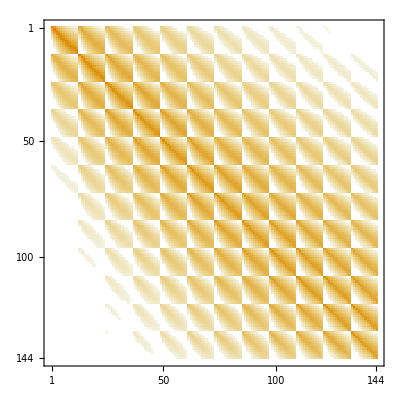

```mathematica
TMtrx[test]//MatrixPlot
```

### Stochastic Dynamics

#### Functions

```mathematica
state[pars_,t_,n0_]:=state[pars,t,n0]=v2m[pars,MatrixPower[TMtrx[pars],t].vec02[pars,n0]]
```

```mathematica
nTot[pars_,t_,n0_]:=Block[{out,x},out={};
For[x=0,x≤nMax[pars],x++,
AppendTo[out,Sum[state[pars,t,n0][[i+1,x-i+1]],{i,0,x}]]
];
out
]
```

```mathematica
nTotAvg[pars_,t_,n0_]:=Block[{out,i,j},
out=0;
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
out+=(i+j)state[pars,t,n0][[i+1,j+1]]
];
];
out
]
```

```mathematica
AF2[pars_,t_,n0_]:=Block[{out,i,j},
out=Table[0,{i,1,10}];
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
If[i+j≠0,
out[[If[i==0,1,Round[(10i)/(i+j)]]]]+=state[pars,t,n0][[i+1,j+1]];
]
];
];
out
]
```

```mathematica
AFAvg[pars_,t_,n0_]:=Block[{out,i,j},
out = 0;
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
If[i+j≠0,
out +=(i/(i+j))state[pars,t,n0][[i+1,j+1]];
]
];
];
out
]
```

#### Plots

```mathematica
meanP1=ListLinePlot[Table[{t/ΔtN,nTotAvg[test,t,{2,2}]},{t,0,tmaxN,ΔtN}],PlotRange->All,PlotStyle->Red];
```

```mathematica
detP1=ListLinePlot[Table[{i/ΔtN,(ndy2[[i+1,2]]+ndy2[[i+1,3]])},{i,0,tmaxN,ΔtN}],PlotRange->All,PlotStyle->Blue];
```

```mathematica
distP1=MatrixPlot[Transpose[Table[0.5-Reverse[nTot[test,t,{2,2}]],{t,0,tmaxN,ΔtN}]],ColorFunction->"GrayTones",AspectRatio->0.5];
```

```mathematica
distP2=MatrixPlot[Transpose[Table[0.5-Reverse[AF2[test,t,{2,2}]],{t,0,tmaxP,ΔtP}]],PlotRange->{{0,10},{0,tmaxP/ΔtP}},AspectRatio->0.5, ColorFunction->"GrayTones"];
```

```mathematica
meanP2=ListLinePlot[Table[{t/ΔtP,10 AFAvg[test,t,{2,2}]},{t,0,tmaxP,ΔtP}],PlotStyle->Red,PlotRange->{Automatic,{0,10}}];
```

```mathematica
detP2=ListLinePlot[Table[{i/ΔtP,10 ndy2[[i+1,2]]/(ndy2[[i+1,2]]+ndy2[[i+1,3]])},{i,0,tmaxP,ΔtP}],PlotRange->All,PlotStyle->Blue];
```

#### Combined Plots

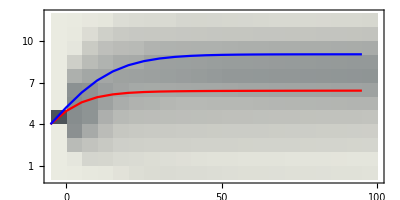

```mathematica
Show[{distP1,meanP1,detP1},FrameTicks->{Table[{t/ΔtN+1,ToString[t]},{t,0,tmaxN,ΔtN*10}],Table[{i,ToString[i]},{i,1,nMax[test],3}],False,False}]
```

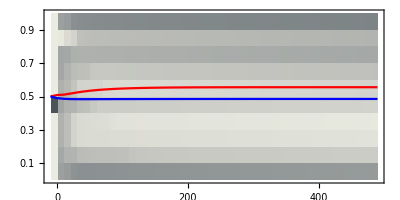

```mathematica
Show[{distP2,meanP2,detP2},FrameTicks->{Table[{t/ΔtP+1,ToString[t]},{t,0,tmaxP,10*ΔtP}],Table[{i,ToString[N[i/10]]},{i,1,10,2}],False,False}]
```

### Stationary distribution

#### Calculating stationary Distribution

```mathematica
Clear[equs,vars]
```

```mathematica
equs[pars_]:=Join[Table[(TMtrx[pars][[2;;,2;;]].Table[Π[i],{i,2,(1+nMax[pars])^2}])[[j-1]]+Π[1] TMtrx[pars][[j-1,1]]==Π[j],{j,2,(1+nMax[pars])^2}],{Total[Table[Π[i],{i,2,(1+nMax[pars])^2}]]==1-Π[1]}]
```

```mathematica
vars[pars_]:=Table[Π[i],{i,1,(1+nMax[pars])^2}]
```

```mathematica
Clear[statDist]
statDist[pars_]:=statDist[pars]=Table[Π[i],{i,1,(1+nMax[pars])^2}]/.Flatten[Chop[NSolve[equs[pars],vars[pars]]]]
```

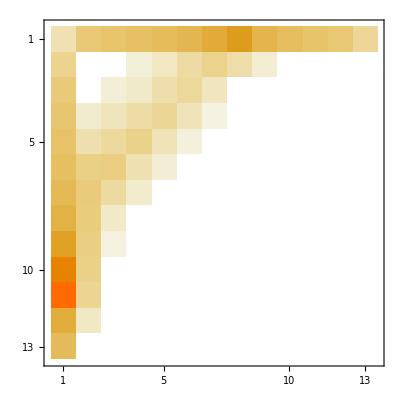

```mathematica
v2m[test,statDist[test]]//MatrixPlot
```

```mathematica
v2m[test,statDist[test]]*Table[i,{i,0,nMax[test]},{j,0,nMax[test]}]//Total//Total
```

8.03943

```mathematica
v2m[test,statDist[test]]*Table[j,{i,0,nMax[test]},{j,0,nMax[test]}]//Total//Total
```

1.01302

```mathematica
nAvg[vec_,pars_]:=Block[{i1,i2,n1,n2},n1=0;n2=0;
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤nMax[pars],i2++,
n1+=vec[[e[i1,i2,pars]]]i1;
n2+=vec[[e[i1,i2,pars]]]i2;
]
];
{n1,n2}
]
```

```mathematica
nAvg[statDist[test],test]
```

{8.03943,1.01302}

#### Functions

```mathematica
nAvg[vec_,pars_]:=Block[{i1,i2,n1,n2},n1=0;n2=0;
For[i1=0,i1≤nMax[pars],i1++,
For[i2=0,i2≤nMax[pars],i2++,
n1+=vec[[e[i1,i2,pars]]]i1;
n2+=vec[[e[i1,i2,pars]]]i2;
]
];
{n1,n2}
]
```

```mathematica
nAvg[statDist[test],test]
```

{8.03943,1.01302}

```mathematica
nTotVec[pars_]:=Block[{statM,i,j,out},out=Table[0,{i,0,2nMax[pars]}];
statM=v2m[pars,statDist[pars]];
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
out[[i+j+1]]+=statM[[i+1,j+1]]
];
];
out
]
```

```mathematica
nTotStatAvg=nTotVec[test].Table[i,{i,0,2nMax[test]}];
```

```mathematica
nTotEquDet=n0[1]+n0[2]/.equSub[1,2]/.{r[0]->r,γ[0]->γ,ms->ϵ m}/.test
```

Solve::svars: Equations may not give solutions for all "solve" variables.

9.49495

```mathematica
pVec[pars_]:=Block[{statM,i,j,out},out=Table[0,{i,1,10}];
statM=v2m[pars,statDist[pars]];
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
out[[If[i==0,1,Round[10 i/(i+j)]]]]+=statM[[i+1,j+1]]
];
];
out
]
```

```mathematica
pMean[pars_]:=Block[{statM,i,j,out},out=0;
statM=v2m[pars,statDist[pars]];
For[i=0,i≤nMax[pars],i++,
For[j=0,j≤nMax[pars],j++,
If[i+j≠0,
out+=i/(i+j)statM[[i+1,j+1]]
]
];
];
out
]
```

```mathematica
pDet=n0[1]/(n0[1]+n0[2])/.equSub[1,2]/.{r[0]->r,γ[0]->γ,ms->ϵ m}/.test
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1.

#### Plots

```mathematica
distP3=MatrixPlot[Transpose[{Reverse[0.5-nTotVec[test][[1;;nMax[test]+1]]]}],ColorFunction->"GrayTones"];
```

```mathematica
meanP3=ListLinePlot[{{0,nTotStatAvg},{1,nTotStatAvg}},PlotStyle->Red,PlotRange->{1,nMax[test]+1}];
```

```mathematica
detP3=ListLinePlot[{{0,nTotEquDet},{1,nTotEquDet}},PlotStyle->Blue,PlotRange->{1,nMax[test]+1}];
```

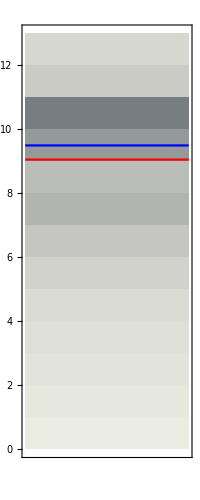

```mathematica
Show[{distP3,meanP3,detP3},FrameTicks->{False,Table[{i,ToString[i]},{i,0,nMax[test]}],False,False}]
```

```mathematica
distP4=MatrixPlot[Transpose[{Reverse[0.5-pVec[test]]}],ColorFunction->"GrayTones"];
```

```mathematica
meanP4=ListLinePlot[{{0,10pMean[test]},{1,10pMean[test]}},PlotStyle->Red,PlotRange->{0,10}];
```

```mathematica
detP4=ListLinePlot[{{0,10pDet},{1,10pDet}},PlotStyle->Blue,PlotRange->{0,10}];
```

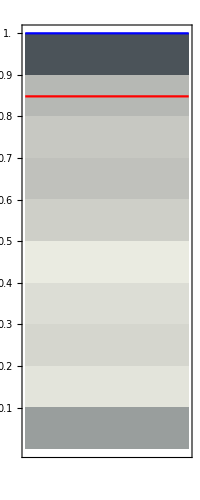

```mathematica
Show[{distP4,detP4,meanP4},FrameTicks->{False,Table[{i,ToString[N[i/10]]},{i,1,10}],False,False}]
```